```mathematica
ClearAll["Global`*"]

(* Script outputs a rational polynomial fit of thermodynamic variables given by lattice qcd eos *)
(* Run cform.sh and then copy-paste fits to equation_of_state class functions in rhic/src/EquationOfState.cpp *)

(* Functions in equation_of_state class (no argument means it's a function of energy density)*)

(* Lattice QCD functions *)
(* equilbrium_pressure *)
(* speed_of_sound_squared() *)
(* effective_temperature()  *)

(* Quasiparticle functions *)
(* z_quasi() *)
(* mdmde_quasi() *)
(* equilibrium_mean_field() *)

(* Shear-bulk relaxation time coefficients. Where/how did I compute these? *)
(* beta_shear(T) *)
(* beta_bulk(T) *)

(* This is in rhic/src/EquationOfState.cpp but not part of equation_of_state class *)
(* equilibrium_energy_density(T) *)

Nf=3;
eg=16.Pi^2/30.;
eq=6.*3*7Pi^2/120.;  (*check these later*)
sFac = eg+eq 

(* plot styles *)
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

(* rational polynomial fit module *)
rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];

tempPts = 450;                                                          (* temperature ranges from 50 to 500 MeV (1 MeV intervals*)
wd=SetDirectory@NotebookDirectory[];
eosData=Import[wd<>"/best_eos.dat"];   (* Subscript[μ, B] = 0 data*)
```

15.6269

```mathematica
(* BEST EoS data columns *)
(* 1 = Subscript[μ, B]    [MeV]  *)
(* 2 = T     [MeV]  *)
(* 3 = P(T)  [fm^-4] *)
(* 4 = s(T)  [fm^-3] *)
(* 6 = e(T)  [fm^-4] *)

MeVtoInversefm =  1./197.326938;   (* convert units from MeV to fm^-1 *)
 eosData[[1,2]]
eosData[[-1,2]]
temp =MeVtoInversefm * eosData[[All,2]];
Tmin = temp[[1]]
Tmax=temp[[-1]]
pressure=eosData[[All,3]];
energy= eosData[[All,6]];
entropy=eosData[[All,4]];

Ptemp=Interpolation[Table[{temp[[i]],pressure[[i]]},{i,1,Length[pressure]}]];
Sfit=Interpolation[Table[{temp[[i]],entropy[[i]]},{i,1,Length[pressure]}]];
etemp=Interpolation[Table[{temp[[i]],energy[[i]]},{i,1,Length[pressure]}]];

emin = etemp[Tmin];
emax=etemp[Tmax];
Print["energy min = ",etemp[Tmin]," fm^-4"]
Print["energy max = ",etemp[Tmax]," fm^-4"]
Print[""]
Print["pressure min = ",Ptemp[Tmin]," fm^-4"]
Print["pressure max = ",Ptemp[Tmax]," fm^-4"]
```

50.

499.

0.253387

2.5288

energy min = 0.00207508 fm^-4

energy max = 525.751 fm^-4

pressure min = 0.000408923 fm^-4

pressure max = 158.987 fm^-4

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

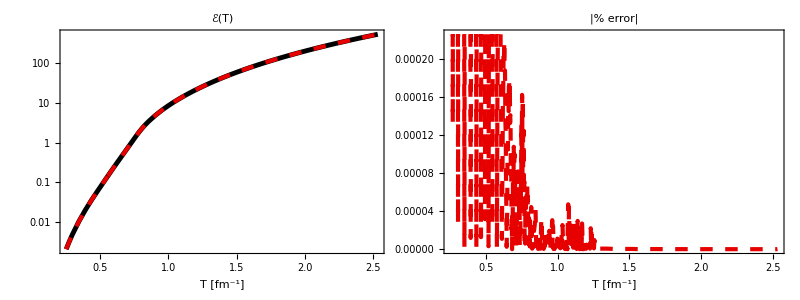

InterpolatingFunction::dmval: Input value {2.53387} lies outside the range of data in the interpolating function. Extrapolation will be used.

530.076

530.076

```mathematica
(*** e(T) fit ***)
edata=Table[{temp[[i]],energy[[i]]},{i,1,Length[pressure]}];
n =20;
efit[T_]=rationalPolyFit[edata,n,n]/.{x->T};

Grid[{{
LogPlot[{etemp[T],efit[T]},{T,Tmin,2.533866},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

Plot[{100*Abs[(etemp[T]-efit[T])/etemp[T]]},{T,Tmin,2.533866},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

etemp[2.533866]
efit[2.533866]
Export["energy.txt",CForm[efit[T]]];
```

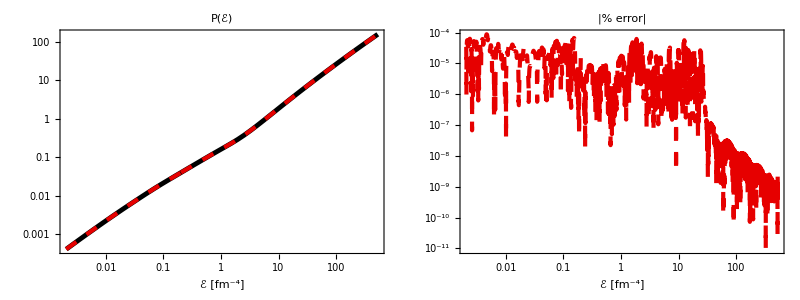

pressure.txt

```mathematica
(*** P(e) fit ***)

Pdata=Table[{etemp[temp[[i]]],Ptemp[temp[[i]]]},{i,1,Length[temp]}];
Pfunc=Interpolation[Pdata];

n =24;
Pfit[e_]=rationalPolyFit[Pdata,n,n]/.{x->e};

Grid[{{
LogLogPlot[{Pfunc[e],Pfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{100*Abs[(Pfunc[e]-Pfit[e])/Pfunc[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["pressure.txt",CForm[Pfit[e]]];
```

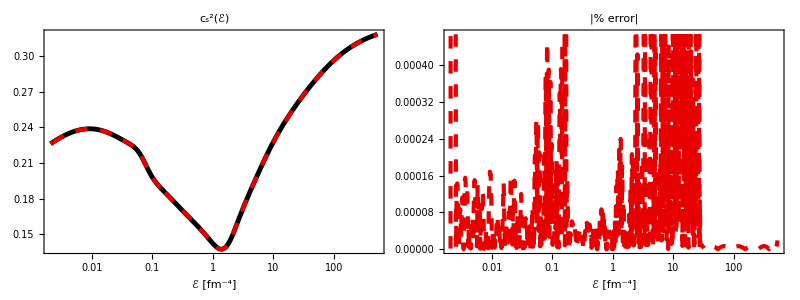

```mathematica
(*** Subscript[c, s]^2(e) fit ***)
(* Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= (e+p)/(T de/dT) *)

cs2temp[T_]=(etemp[T]+Ptemp[T])/(T*etemp'[T]);
cs2data=Table[{etemp[temp[[i]]],cs2temp[temp[[i]]]},{i,1,Length[temp]}];
cs2func=Interpolation[cs2data];

n =22;
cs2fit[e_]=rationalPolyFit[cs2data,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{cs2func[e],cs2fit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLinearPlot[{100*Abs[(cs2func[e]-cs2fit[e])/cs2func[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["cs2.txt",CForm[cs2fit[e]]];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

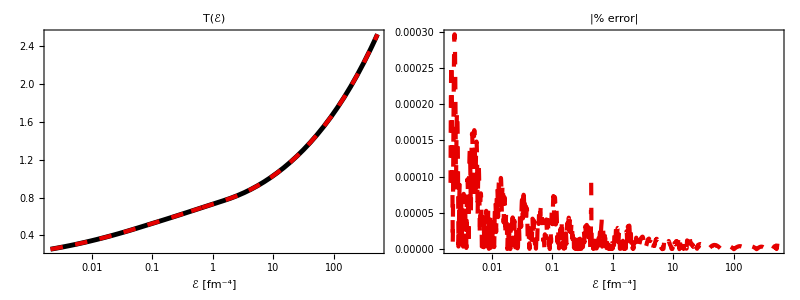

```mathematica
(*** T(e) fit ***)

Tdata=Table[{etemp[temp[[i]]],temp[[i]]},{i,1,Length[temp]}];
Tfunc=Interpolation[Tdata];

n =20;
Tfit[e_]=rationalPolyFit[Tdata,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLinearPlot[{100*Abs[(Tfunc[e]-Tfit[e])/Tfunc[e]]},{e,emin,emax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["temperature.txt",CForm[Tfit[e]]];
```

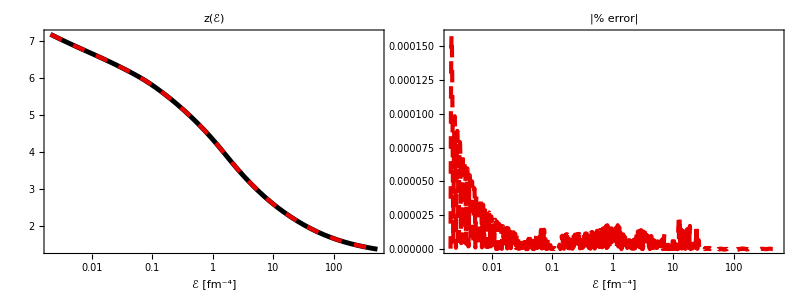

```mathematica
(*** z(e) fit ***)

nc = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*Nf);
F[T_]=(2.0*Pi^2)/g*Sfit[T]/T^3;

zQuasi=Table[{temp[[i]],""},{i,1,Length[temp]}];
zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[450]]],{x,1.3},MaxIterations->5000];

For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]
zQuasitemp=Interpolation[zQuasi];

zQuasidata=Table[{etemp[temp[[i]]],zQuasitemp[temp[[i]]]},{i,1,Length[temp]}];
zQuasifunc=Interpolation[zQuasidata];

n =22;
zQuasifit[e_]=rationalPolyFit[zQuasidata,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{zQuasifunc[e],zQuasifit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["z(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLinearPlot[{100*Abs[(zQuasifunc[e]-zQuasifit[e])/zQuasifunc[e]]},{e,emin,emax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["zquasi.txt",CForm[zQuasifit[e]]];
```

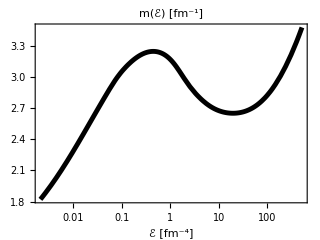

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

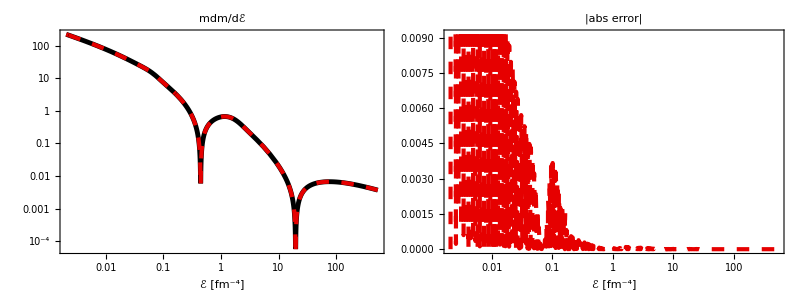

```mathematica
(*** m dm/de fit ***) 

mQuasifunc[e_] =Tfunc[e]*zQuasifunc[e]; 
LogLinearPlot[{mQuasifunc[e]},{e,emin,emax},PlotStyle->styles[[1]],ImageSize->320,Frame->True,PlotLabel->Style["m(ℰ) [fm^-1]",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]

mdmde[e_]=mQuasifunc[e]*mQuasifunc'[e];
mdmdedata=Table[{etemp[temp[[i]]],mdmde[etemp[temp[[i]]]]},{i,1,Length[temp]}];

n =26;
mdmdefit[e_]=rationalPolyFit[mdmdedata,n,n]/.{x->e};

Grid[{{LogLogPlot[{Abs[mdmde[e]],Abs[mdmdefit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLinearPlot[{Abs[(mdmde[e]-mdmdefit[e])]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|abs error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["mdmde.txt",CForm[mdmdefit[e]]];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

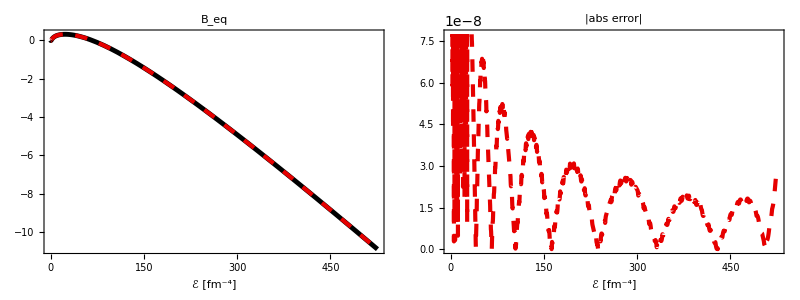

```mathematica
(*** Subscript[B, eq](ℰ) fit ***)

Pquasi[e_]=(g*Tfunc[e]^4)/(2.*Pi^2)*zQuasifunc[e]^2*BesselK[2,zQuasifunc[e]];

B0Quasi=Table[{etemp[temp[[i]]],Pquasi[etemp[temp[[i]]]]-Pfunc[etemp[temp[[i]]]]},{i,1,Length[temp]}];
B0Quasifunc=Interpolation[B0Quasi];

n =20;
B0Quasifit[e_]=rationalPolyFit[B0Quasi,n,n]/.{x->e};

Grid[{{
Plot[{B0Quasifunc[e],B0Quasifit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{Abs[B0Quasifunc[e]-B0Quasifit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|abs error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

(*Plot[{B0Quasifunc[etemp[T]],B0Quasifit[etemp[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]*)

Export["Beq.txt",CForm[B0Quasifit[e]]];
```

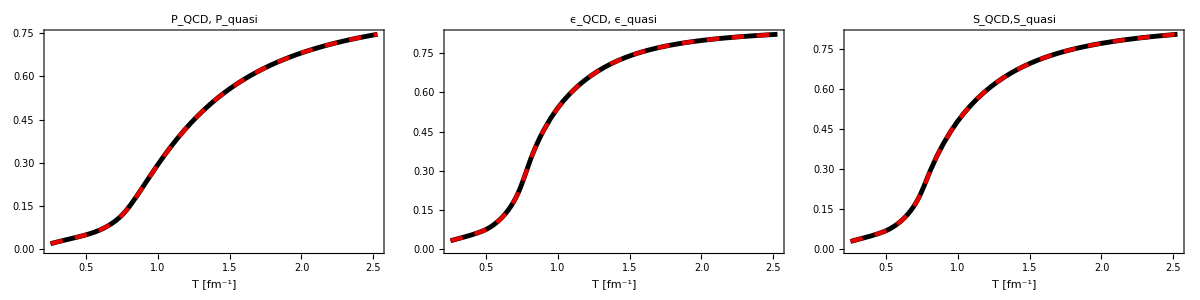

```mathematica
(* check thermodynamic consistency *)
Pquasi[e_]=(g*Tfunc[e]^4)/(2.0*Pi^2)*zQuasifunc[e]^2*BesselK[2,zQuasifunc[e]] -B0Quasifunc[e];
Equasi[e_]=(g*Tfunc[e]^4)/(2.0*Pi^2)*zQuasifunc[e]^2*(3.0*BesselK[2,zQuasifunc[e]]+zQuasifunc[e]*BesselK[1,zQuasifunc[e]])+B0Quasifunc[e];

SQuasi[e_]=(Pquasi[e]+Equasi[e])/Tfunc[e];

Grid[{{Plot[{Ptemp[T]/(sFac T^4/3),Pquasi[etemp[T]]/(sFac T^4/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{etemp[T]/(sFac T^4),Equasi[etemp[T]]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Sfit[T]/(4*sFac*T^3/3),SQuasi[etemp[T]]/(4*sFac*T^3/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

```mathematica
(* not sure what's going on here *)
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 14;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*Sfit[T]*T;

Grid[{{Plot[{betapi[T],betapifit[T]},{T,temp[[1]],temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*Sfit[T]),betapiconformal[T]/(T*Sfit[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 18;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*T*Sfit[T];

betapifit[temp[[450]]]

betapiold[T_]=(8.611704298094825*10^-6-0.001405354006113392*T+0.059924402660583354*T^2-1.1252821226321765*T^3+11.505088678768702*T^4-72.86243933500441*T^5+312.67652000568955*T^6-919.4553300642775*T^7+1851.880055174282*T^8-2520.2910195876684*T^9+2228.4719999229687*T^10-1163.3696941415265*T^11+275.1649200477449*T^12)/(4.814184219646834-23.427763291345297*T+78.10907293901035*T^2-220.9834748507111*T^3+463.6211365026477*T^4-658.0962754530466*T^5+604.0491642749903*T^6-329.15455711633166*T^7+83.03984882593176*T^8-0.34262854377950497*T^9+0.03765047242502595*T^10-0.0024572359354327667*T^11+0.0000720828838022736*T^12);

Grid[{{Plot[{betapiold[T],betapifit[T]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*Sfit[T]),betapiconformal[T]/(T*Sfit[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

122.159

```mathematica
(* betabulk =5.0*betapi/3.0-cs2*(e+p)+cs2*mdmdT*I11 *)

Clear[betabulk,betabulkData,betabulkfit,I11DataRaw,I11Data,I11]

I11DataRaw=Import[wd<>"/betabulkplot.dat"];
I11Data= Take[I11DataRaw,{2,Length[I11DataRaw]}];
I11 = Interpolation[I11Data[[All,{1,2}]]];

betabulk[T_]=5.0/3.0*betapi[T]+cs2fit[etemp[T]]*(mdmdTQuasi[T]*I11[T]-(etemp[T]+Ptemp[T]));

betabulkData=Table[{T,betabulk[T]},{T,Tmin,Tmax,0.001}];
betabulk=Interpolation[betabulkData];

n = 18;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};


betabulkold[T_]=(0.057187918268175174-2.5795110808844144*T+31.966143337661794*T^2-186.97202223464143*T^3+632.9739160169219*T^4-1356.8644912535221*T^5+1937.6556428262882*T^6-1901.4144609887912*T^7+1305.7115016142484*T^8-632.7107309491553*T^9+215.7883928137199*T^10-50.783337922429304*T^11+7.882963305898372*T^12-0.7302386364254765*T^13+0.031006456705249083*T^14)/(2168.5818494848654-17367.372494454743*T+62866.89323544513*T^2-136008.52657020878*T^3+196076.0893015133*T^4-198954.9682758633*T^5+146384.87731197142*T^6-79310.95783243925*T^7+31803.091369445476*T^8-9398.242646642117*T^9+2016.6245278736917*T^10-304.98512854363526*T^11+30.758339605713708*T^12-1.852389925261096*T^13+0.05027444936020055*T^14);

betabulkconformal[T_]=14.55*(1.0/3.0-cs2fit[T])^2*(etemp[T]+Ptemp[T]);

Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betabulk[T]-betabulkfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
(*,Plot[{betabulkfit[T]/(etemp[T]+Ptemp[T]),betabulkconformal[T]/(etemp[T]+Pfit[T])},{T,temp[[1]],temp[[400]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]*)}}]

betabulkfit[T]//CForm
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.